```mathematica
Copyright © 2021 Franz Utermohlen. All rights reserved.
```

Description: Finds the eigenvalues and eigenvectors of an N-site, spin-s (where s=1/2 or 1) chain with XYZ Hamiltonian:
			H_XYZ=∑_(<ij>) (J_x S_i^x S_j^x+(J_y S)_i^y S_j^y+(J_z S)_i^z S_j^z) .
Optional: Add a local magnetic field of strength h_local at site 0, and/or a global magnetic field of strength h_global at all the sites:
			H_local=-h_local S_0^z ,	H_global=-h_global(∑_i S)_i^z .
Inputs: spin, numSites, Jx, Jy, Jz, hglobal, hlocal, boundaryConditions.

```mathematica
(* INPUTS BELOW *)

(*Spin of the sites (either 1/2 or 1)*)
spin=1/2;
(*Number of sites in the chain*)
numSites=4;
(*Coupling constants*)
Jx=Jy=Jz=1;
(*Jx=Jy=-0.9;*)
(*Magnitude of global and local magnetic fields*)
hglobal=0;
hlocal=0;
(*Boundary conditions: 0 for open, and 1 for periodic boundary conditions*)
boundaryConditions=1;

(* --- *)

(*Dimension of the spin Hilbert space for a single site*)
dim=2spin+1;
(*Create empty Hamiltonian matrix ham*)
ham=SparseArray[ConstantArray[0.,{dim^numSites,dim^numSites}]];
(*Create vector S=(Sx,Sy,Sz) containing the 3 spin matrices*)
(*For spin=1/2*)
If[spin==1/2,
S=1/2(SparseArray/@(PauliMatrix/@{1,2,3}));
];
(*For spin=1*)
If[spin==1,
S=SparseArray/@{1/Sqrt[2]({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),1/(ⅈ Sqrt[2])({{0, 1, 0}, {-1, 0, 1}, {0, -1, 0}}),({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}})};
];
(*Create vector J=(Subscript[J, x],Subscript[J, y],Subscript[J, z]) containing the coupling constants*)
J={Jx,Jy,Jz};
(*Create a list of numSites dim-by-dim identity matrices. For example, for spin=1/2 and numSites=4, list is a list of four 2x2 identity matrices*)
list=Table[SparseArray[IdentityMatrix[dim]],numSites];

(*Add all of the open boundary terms*)
Do[
Do[
list[[k]]=list[[k+1]]=S[[α]];
SiαSjα=KroneckerProduct[Sequence@@list];
ham+=J[[α]]SiαSjα;
,
{α,3} (*α sums over x, y and z*)
];

list[[k]]=list[[k+1]]=SparseArray[IdentityMatrix[dim]];
,
{k,numSites-1}
];

(*Add the periodic boundary term if the chain has 3 or more sites*)
If[boundaryConditions==1&&numSites≥3,
Do[
list[[1]]=list[[numSites]]=S[[α]];
SiαSjα=KroneckerProduct[Sequence@@list];
ham+=J[[α]]SiαSjα;
,
{α,3}
];

list[[1]]=list[[numSites]]=SparseArray[IdentityMatrix[dim]];
];

(*Add the local magnetic field term (acting on site 0)*)
If[hlocal≠0,
list[[1]]=S[[3]];
S0z=KroneckerProduct[Sequence@@list];
ham-=hlocal S0z;

list[[1]]=SparseArray[IdentityMatrix[dim]];
];

(*Add the global magnetic field terms*)
If[hglobal≠0,
Do[
list[[k]]=S[[3]];
Siz=KroneckerProduct[Sequence@@list];
ham-=hglobal Siz;

list[[k]]=SparseArray[IdentityMatrix[dim]];
,
{k,numSites}
];
];

(*Get rid of infinitesimal quantities*)
ham=Chop/@ham;

(*Find eigenvalues and eigenvectors*)
{energyvals,energyvecs}=Chop/@Eigensystem[N[ham]];
energyvals=Re[energyvals];
(*Get rid of infinitesimal discrepancies between the energy states*)
Do[
energyvals=Chop[energyvals-energyvals[[ii]]]+energyvals[[ii]];
,{ii,1,Length[energyvals]}];
(*Arrange energy eigenvalues and energy eigenvectors in order from lowest energy to highest energy*)
energyvecs=energyvecs[[Ordering[energyvals]]];
energyvals=energyvals[[Ordering[energyvals]]];
(*Energy eigenvalues per site (E/N)*)
energyvalsPerSite=energyvals/numSites;

(*Ground states*)
gsenergy=Min[energyvalsPerSite]; (*per site*)
gsindices=Flatten[Position[energyvalsPerSite,gsenergy]];
gsnum=Length[gsindices]; (*number of ground states*)
gsvecs=energyvecs[[gsindices]];
(*One of the ground states*)
gs=gsvecs[[1]];
(*First excited states*)
fexcenergy=energyvalsPerSite[[1+Length[gsindices]]]; (*per site*)
fexcindices=Flatten[Position[energyvalsPerSite,fexcenergy]];
fexcnum=Length[fexcindices]; (*number of first excited states*)
fexcvecs=energyvecs[[fexcindices]];
(*One of the first excited states*)
fexc=fexcvecs[[1]];

(*
(*Convert the ground state to more readable ket notation where we specify the value of Subscript[S, z] at each site*)
gsKetNotation=0;
Do[
If[gs[[i]]≠0,
gsKetNotation=gsKetNotation+gs[[i]]Ket[
If[spin==1/2,
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"↑","1"->"↓"}],
(*else, for spin==1*)
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"+","1"->"0","2"->"-"}]
]
]
]
,{i,Length[gs]}];

gsKetNotation
*)
```

```mathematica
gsvecs
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Equal-time spin-spin correlation function ⟨S_k^z(0)S_0^z(0)⟩:

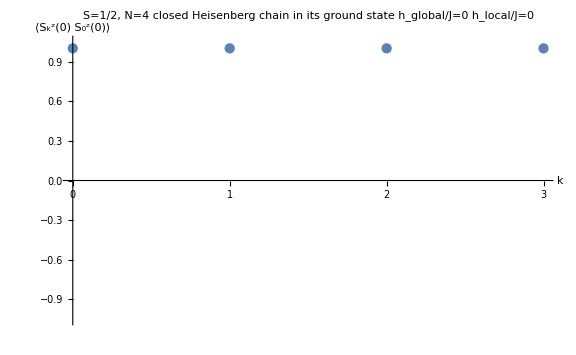

```mathematica
(*Choose the state we want to compute the expectation value in (either gs or fexc, where gs is a ground state and fexc is a first excited state)*)
state=gs;
(*state=fexc;*)
(*==========================================*)
(*Initialize spinspinCorr*)
spinspinCorr=ConstantArray[0,numSites];
(*Create list*)
list=Table[SparseArray[IdentityMatrix[dim]],numSites];
(*Compute the equal-time spin-spin correlation function ⟨Subscript[S, k]^z Subscript[(0)S, 0]^z(0)⟩ for all values of k*)
Do[
If[k≠0,
list[[1]]=list[[k+1]]=S[[3]];
,(*else, if k=0*)
list[[1]]=S[[3]].S[[3]];
];
SkS0=KroneckerProduct[Sequence@@list];
spinspinCorr[[k+1]]=Chop[state.SkS0.state];

list[[1]]=list[[k+1]]=SparseArray[IdentityMatrix[dim]];
,
{k,0,numSites-1}
];
(*Normalize ⟨Subscript[S, k]^z Subscript[(0)S, 0]^z(0)⟩*)
normalization=spinspinCorr[[1]];
spinspinCorr/=normalization;

(*Make a data table for ⟨Subscript[S, k]^z Subscript[(0)S, 0]^z(0)⟩*)
data=Transpose[{Range[numSites]-1,spinspinCorr}];
(*Plot ⟨Subscript[S, k]^z Subscript[(0)S, 0]^z(0)⟩*)
ListPlot[data,PlotLabel->"S="<>ToString[spin,InputForm]<>", N="<>ToString[numSites]<>ToString[If[boundaryConditions==1," closed"," open"]]<>" Heisenberg chain in its "<>ToString[If[state==gs,"ground ","first excited "]]<>"state\nh_global/J="<>ToString[hglobal]<>"\th_local/J="<>ToString[hlocal],Ticks->{Range[numSites]-1,Automatic},AxesLabel->{Style[HoldForm[k],FontSize->18],Style[HoldForm[⟨Subscript[S, k]^z(0)Subscript[S, 0]^z(0)⟩],FontSize->15]},PlotRange->{Automatic,{-1.05,1.05}},ImageSize->Large,LabelStyle->Directive[12,Bold]]

(*
(*Plot with manual fit for 11 sites*)
Plot[Cos[3.13 k]/(1.06)^(6k),{k,0,numSites-1},Epilog->Map[Point,data],AxesLabel->{Style[HoldForm[k],FontSize->20],Style[HoldForm[⟨Subscript[S, k]^z(0)Subscript[S, 0]^z(0)⟩],FontSize->15]},PlotRange->{Automatic,{-1.05,1.05}},ImageSize->Large]
*)

(*
Clear[a,k];
(*Plot with fit*)
model=Cos[k a]Exp[-k/ξ]; (*k is the site index*)
fit=FindFit[spinspinCorr,model,{a,ξ},k];
modelf=Function[{k},Evaluate[model/.fit]];
Plot[modelf[k],{k,0,numSites-1},Epilog->Map[Point,data],PlotRange->{Automatic,{-1,1}},Ticks->{Range[numSites]-1,Automatic}]
*)

(*
(*Choose site k*)
k=0;
(*Initialize spinspinCorr*)
spinspinCorr=ConstantArray[0,numSites];
(*Reset the list array*)
list=Table[SparseArray[IdentityMatrix[dim]],numSites];
(*Compute the equal-time spin-spin correlation function for site k*)
(*Initialize Subscript[S, k]^z Subscript[S, 0]^z*)
SkS0=SparseArray[ConstantArray[0,{dim^numSites,dim^numSites}]];
(*Compute Subscript[S, k]^z Subscript[S, 0]^z*)
If[k≠0,
Do[
list[[1]]=list[[k+1]]=S[[j]];
SkS0=SkS0+KroneckerProduct[Sequence@@list];
list[[1]]=list[[k+1]]=SparseArray[IdentityMatrix[dim]];
,
{j,3}
]
,(*else, if k=0*)
Do[
list[[1]]=S[[j]].S[[j]];
SkS0=SkS0+KroneckerProduct[Sequence@@list];
list[[1]]=SparseArray[IdentityMatrix[dim]];
,
{j,3}
]
];
(*Compute ⟨Subscript[S, k]^z Subscript[S, 0]^z⟩/(S(S+1)) in the ground state*)
spinspinCorr[[k+1]]=Chop[Conjugate[gs].SkS0.gs/(spin(spin+1))]
*)
```

Dynamic spin-spin autocorrelation function ⟨S_k^z(t)S_j^z(0)⟩:

```mathematica
(*Choose the state we want to compute the expectation value in (either gs or fexc, where gs is a ground state and fexc is a first excited state)*)
state=gs;
(*state=fexc;*)
(*Choose site j (where 0<j<(numSites-1))*)
j=0;
(*Choose the maximum time reached maxTime and the interval between time steps Δt*)
maxTime=20;
Δt=0.01;
(*==========================================*)
(*Find the number of time steps needed to get from t=0 to t=maxTime in intervals Δt*)
nTimeSteps=maxTime/Δt+1;
(*Initialize spinspinCorr*)
spinspinCorr=Table[0,nTimeSteps];
(*Initialize dataRe*)
dataRe=Table[0,numSites];
(*Create list*)
list=Table[SparseArray[IdentityMatrix[dim]],numSites];
(*Create the Subscript[S, j]^z(0) operator*)
list[[j+1]]=S[[3]];
Sj0=KroneckerProduct[Sequence@@list];
list[[j+1]]=SparseArray[IdentityMatrix[dim]];
(*Loop over all possible values of k*)
Do[
(*Create the Subscript[S, k]^z(0) operator (same as above, but for k)*)
list[[k+1]]=S[[3]];
Sk0=KroneckerProduct[Sequence@@list];
list[[k+1]]=SparseArray[IdentityMatrix[dim]];
(*Initialize the time step index timeStep*)
timeStep=1;
(*Compute the dynamic spin-spin autocorrelation function*)
Do[
(*Compute the time evolution operator U for the current time t*)
U=MatrixExp[N[-ⅈ ham t]];
(*Create the Subscript[S, k]^z(t) operator*)
Skt=SparseArray[ConjugateTranspose[U].Sk0.U];
SktSj0=Skt.Sj0;
(*Compute ⟨Subscript[S, k]^z(t)Subscript[S, j]^z(0)⟩ for the current time t*)
spinspinCorr[[timeStep]]=Chop[Conjugate[state].SktSj0.state];
(*Update timeStep*)
timeStep+=1;
,
{t,0,maxTime,Δt}
];
(*Normalize ⟨Subscript[S, k]^z(t)Subscript[S, j]^z(0)⟩*)
If[k==j,
normalization=spinspinCorr[[1]];
];
(*Note: even though it might seem like this If statement would break the code if j≠0 (since normalization won't be defined in the loop for all k<j), it does work, because Mathematica replaces the unknown normalization variable with the numerical value of normalization once it finds it!. (It also turns out to be faster than doing it the "proper" way too.)*)
spinspinCorr/=normalization;

(*Make data tables for the real and imaginary parts of the dynamic autocorrelation function <Subscript[S, k]^z(t)Subscript[S, j]^z(0)>*)
dataRe[[k+1]]=Transpose[{Range[0,maxTime,Δt],Re[spinspinCorr]}];
(*dataIm[[k+1]]=Transpose[{Range[0,maxTime,Δt],Im[spinspinCorr]}];*)
,
{k,0,numSites-1}
];
```

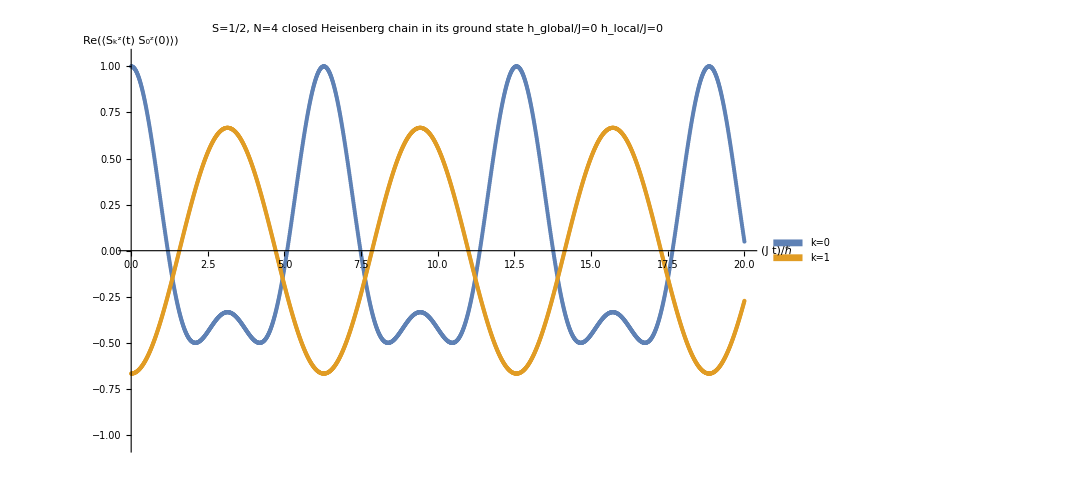

```mathematica
(*Choose which values of k to plot*)
kplot={0,1};

(*Plot the real part of <Subscript[S, k]^z(t)Subscript[S, j]^z(0)>*)
ListPlot[dataRe[[kplot+1]],PlotLabel->"S="<>ToString[spin,InputForm]<>", N="<>ToString[numSites]<>ToString[If[boundaryConditions==1," closed"," open"]]<>" Heisenberg chain in its "<>ToString[If[state==gs,"ground ","first excited "]]<>"state\nh_global/J="<>ToString[hglobal]<>"\th_local/J="<>ToString[hlocal],AxesLabel->{Style[HoldForm[("J t")/("ℏ")],FontSize->22],Style[HoldForm[Re[⟨Subscript[S, k]^z(t)Subscript[S, 0]^z(0)⟩]],FontSize->15]},LabelStyle->Directive[12,Bold],ImageSize->800,PlotRange->{Automatic,{-1.05,1.05}},PlotLegends->SwatchLegend[Table["k="<>ToString[kplot[[n]]],{n,1,Length[kplot]}]]]
```

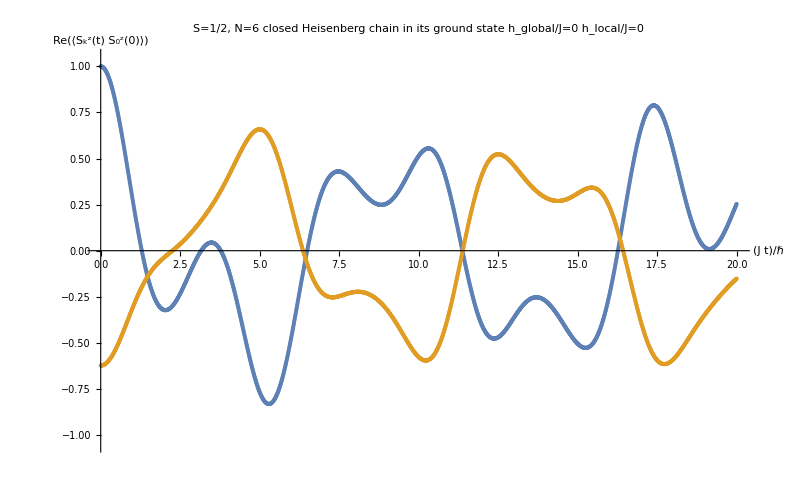

Dynamic structure factor S^αβ(k,ω)=∫_(-∞)^∞ ⅇ^ⅈωt⟨S_k^α(t)S_-k^β(0)⟩dt/(2π):

```mathematica
(*Choose the state we want to compute the expectation value in (either gs or fexc, where gs is a ground state and fexc is a first excited state)*)
state=gs;
(*state=fexc;*)
(*Choose the number of steps nTimeSteps*)
nTimeSteps=40;
(*Choose α and β (where α,β are spin component labels; 1 is x, 2 is y, 3 is z*)
α=3;
β=3;
(*==========================================*)
Clear[k];
(*Create list*)
list=Table[SparseArray[IdentityMatrix[dim]],numSites];
(*Create the Subscript[S, i]^α(0) and Subscript[S, j]^β(0) operators*)
Siα=Sjβ=ConstantArray[0,numSites];
Do[
list[[i+1]]=S[[α]];
Siα[[i+1]]=KroneckerProduct[Sequence@@list];
list[[i+1]]=S[[β]];
Sjβ[[i+1]]=KroneckerProduct[Sequence@@list];
list[[i+1]]=SparseArray[IdentityMatrix[dim]];
,{i,0,numSites-1}];
(*Create the Subscript[S, k]^α(0) and Subscript[S, -k]^β(0) operators, given by Subscript[S, k]^α(0)=1/(√N)∑_n e^Subscript[ikr, n] Subscript[S, n]^α(0)*)
Skα0=Smkβ0=0;
Do[
Skα0=Skα0+Exp[ⅈ k n]Siα[[n+1]];
Smkβ0=Smkβ0+Exp[-ⅈ k n]Sjβ[[n+1]];
,{n,0,numSites-1}];
Skα0=Skα0/Sqrt[numSites];
Smkβ0=Smkβ0/Sqrt[numSites];
(*Initialize the data to be numerically integrated dataToIntegrate*)
dataToIntegrate=ConstantArray[0,nTimeSteps];
(*Max time*)
τMax=1-10^(-4);
(*Find the time interval Δτ between time steps, where τ denotes parametrized time (which runs from -1 to 1), and t denotes real time (which runs from -∞ to ∞)*)
Δτ=2τMax/(nTimeSteps-1);
(*Initialize the time step index timeStep*)
timeStep=1;
Do[
(*Find the real time t for the current parametrized time τ*)
t=τ/(1-τ^2);
(*Compute the time evolution operator U for the current time t*)
U=MatrixExp[N[-ⅈ ham t]];
(*Create the Subscript[S, k]^z(t) operator*)
Skαt=SparseArray[ConjugateTranspose[U].Skα0.U];
SkαtSmkβ0=Skαt.Smkβ0;
(*Compute ⟨Subscript[S, k]^z(t)Subscript[S, j]^z(0)⟩ for the current time t*)
dataToIntegrate[[timeStep]]=((1+t^2)/(1-t^2)^2)Exp[ⅈ ω t]Chop[Conjugate[state].SkαtSmkβ0.state];
(*Update timeStep*)
timeStep+=1;
,
{τ,-τMax,τMax,Δτ}
];
(*Initialize the dynamic structure factor dynamicStrucFac*)
dynamicStrucFac=0;
(*Perform integration using the trapezoidal rule*)
timeStep=1;
Do[
dynamicStrucFac=dynamicStrucFac+Δτ(dataToIntegrate[[timeStep]]+dataToIntegrate[[timeStep+1]])/2;
timeStep+=1;
,
{τ,-τMax,τMax-Δτ,Δτ}
];
dynamicStrucFac=dynamicStrucFac/(2Pi);

(*ContourPlot[dynamicStrucFac,{k,0,2π},{ω,0,3},
FrameLabel->{ka,ω/"J?"},
FrameTicks->{{0,π,2π},Automatic}]*)
(*Plot3D[dynamicStrucFac,{k,-10,10},{ω,-10,10}(*,PlotRange->{{-1,1},{-1,1}}*)]*)
```

S_tot^2 operator:

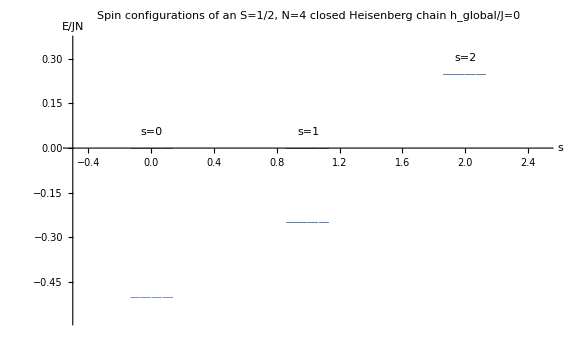

```mathematica
(*Initialize StotSq*)
StotSq=SparseArray[ConstantArray[0,{dim^numSites,dim^numSites}]];
(*Compute StotSq*)
Do[
Do[
If[i≠j,
Do[
list[[i]]=list[[j]]=S[[α]];
SiαSjα=KroneckerProduct[Sequence@@list];
StotSq=StotSq+SiαSjα;
,
{α,3}
];
list[[i]]=list[[j]]=SparseArray[IdentityMatrix[dim]];
,(*else*)
StotSq=StotSq+spin(spin+1)SparseArray[IdentityMatrix[dim^numSites]];
];
,
{j,numSites}
];
,
{i,numSites}
];

(*Get rid of infinitesimal quantities*)
StotSq=Chop/@StotSq;
(*Find total spin eigenvalues/eigenvectors*)
{StotSqVals,StotSqvecs}=Chop/@Eigensystem[N[StotSq]];
StotSqVals=Round[StotSqVals,1/4];
(*Convert the entries in StotSqVals, which are of the form s(s+1), to the form s; store these in a new list StotVals*)
StotVals=Table[0.,Length[StotSqVals]];
spinRelationList=Table[{s(s+1),s},{s,0,numSites spin,spin}];
Do[
StotVals[[k]]=spinRelationList[[All,2]][[(FirstPosition[spinRelationList[[All,1]],StotSqVals[[k]]][[1]])]];
,
{k,dim^numSites}
];
(*Arrange eigenvalues and eigenvectors in order from lowest Stot to highest Stot*)
StotSqvecs=StotSqvecs[[Ordering[StotVals]]];
StotVals=StotVals[[Ordering[StotVals]]];

(*Find the different possible values of Stot*)
differentStot=Union[StotVals];
(*Find dimensionStot; dimensionStot[[i]] gives the total dimension of the spin sector corresponding to Subscript[s, tot]=differentStot[[i]]*)
dimensionStot=Table[0,Length[differentStot]];
Do[
dimensionStot[[kk]]=Count[StotVals,differentStot[[kk]]];
,{kk,Length[differentStot]}];

(*Block diagonalize the Hamiltonian in the StotSq basis*)
U=Transpose[StotSqvecs];
hamDiag=Chop[Inverse[U].ham.U,10^-9];
hamBlock=hamDiag;
(*Diagonalize each block individually*)
blockStart=1;
Do[
blockEnd=blockStart+dimensionStot[[i]]-1;
If[dimensionStot[[i]]≠1,
hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]=DiagonalMatrix[Sort[Re[Eigenvalues[hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]]]]];
(*
U=Transpose[Eigenvectors[hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]]];
hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]=Chop[Inverse[U].hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]].U];
*)
];
blockStart=blockEnd+1;
,{i,Length[dimensionStot]}];

(*Energy eigenvalues*)
energyvals=Chop[Diagonal[hamDiag]];
(*Get rid of infinitesimal discrepancies between the energy states*)
Do[
energyvals=Chop[energyvals-energyvals[[j]]]+energyvals[[j]];
,{j,1,Length[energyvals]}];
(*Energy eigenvalues per site (E/N)*)
energyvalsPerSite=energyvals/numSites;

(*Energy level diagram*)
data=Transpose[{StotVals,energyvalsPerSite}];
listOfSpins=Union[StotVals];
spinAxisMin=Min[listOfSpins]-1/2;
spinAxisMax=Max[listOfSpins]+1/2;

deltaE=Max[energyvalsPerSite]-Min[energyvalsPerSite];
energyAxisMin=Min[energyvalsPerSite]-deltaE/10;
energyAxisMax=Max[energyvalsPerSite]+deltaE/7;
Show[
ListPlot[data,ImageSize->Large,AxesLabel->{"s",HoldForm[("E")/("JN")]},LabelStyle->Directive[12,Bold],PlotLabel->"Spin configurations of an S="<>ToString[spin,InputForm]<>", N="<>ToString[numSites]<>ToString[If[boundaryConditions==1," closed"," open"]]<>" Heisenberg chain\nh_global/J="<>ToString[hglobal],
PlotMarkers->"————",AxesOrigin->{spinAxisMin,0},Axes->{False,True},PlotRange->{{spinAxisMin,spinAxisMax},{energyAxisMin,energyAxisMax}}],
Table[
Graphics[
Text["s="<>ToString[listOfSpins[[k]],InputForm],{listOfSpins[[k]],energyvalsPerSite[[dim^numSites+1-FirstPosition[Reverse[StotVals],listOfSpins[[k]]][[1]]]]+deltaE/14},BaseStyle->{FontSize->17}]
]
,{k,Length[listOfSpins]}]
]
```

S_(z,tot) operator:

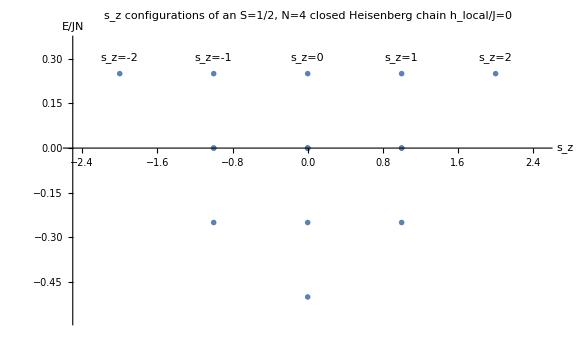

```mathematica
(*Initialize Sztot*)
Sztot=SparseArray[ConstantArray[0,{dim^numSites,dim^numSites}]];
(*Compute Sztot*)
Do[
list[[i]]=S[[3]];
Siz=KroneckerProduct[Sequence@@list];
Sztot=Sztot+Siz;

list[[i]]=SparseArray[IdentityMatrix[dim]];
,
{i,numSites}
];

(*Get rid of infinitesimal quantities*)
Sztot=Chop/@Sztot;
(*Find spin eigenvalues/eigenvectors*)
{SztotVals,Sztotvecs}=Chop/@Eigensystem[N[Sztot]];
(*Arrange eigenvalues and eigenvectors in order from lowest Sz to highest Sz*)
Sztotvecs=Sztotvecs[[Ordering[SztotVals]]];
SztotVals=Round[SztotVals[[Ordering[SztotVals]]]];

(*Find the different possible values of Stot*)
differentSztot=Union[SztotVals];
(*Find dimensionStot; dimensionStot[[i]] gives the total dimension of the spin sector corresponding to Subscript[s, tot]=differentStot[[i]]*)
dimensionSztot=Table[0,Length[differentSztot]];
Do[
dimensionSztot[[kk]]=Count[SztotVals,differentSztot[[kk]]];
,{kk,Length[differentSztot]}];

(*Block diagonalize the Hamiltonian in the Sztot basis*)
U=Transpose[Sztotvecs];
hamDiag=Chop[Inverse[U].ham.U,10^-9];
hamBlock=hamDiag;
(*Diagonalize each block individually*)
blockStart=1;
Do[
blockEnd=blockStart+dimensionSztot[[i]]-1;
If[dimensionSztot[[i]]≠1,
hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]=DiagonalMatrix[Sort[Re[Eigenvalues[hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]]]]];
(*
U=Transpose[Eigenvectors[hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]]];
hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]]=Chop[Inverse[U].hamDiag[[blockStart;;blockEnd,blockStart;;blockEnd]].U];
*)
];
blockStart=blockEnd+1;
,{i,Length[dimensionSztot]}];

(*Energy eigenvalues*)
energyvals=Chop[Diagonal[hamDiag]];
(*Get rid of infinitesimal discrepancies between the energy states*)
Do[
energyvals=Chop[energyvals-energyvals[[j]]]+energyvals[[j]];
,{j,1,Length[energyvals]}];
(*Energy eigenvalues per site (E/N)*)
energyvalsPerSite=energyvals/numSites;

(*Energy level diagram*)
data=Transpose[{SztotVals,energyvalsPerSite}];
listOfSpins=Union[SztotVals];
spinAxisMin=Min[listOfSpins]-1/2;
spinAxisMax=Max[listOfSpins]+1/2;

deltaE=Max[energyvalsPerSite]-Min[energyvalsPerSite];
energyAxisMin=Min[energyvalsPerSite]-deltaE/10;
energyAxisMax=Max[energyvalsPerSite]+deltaE/7;
If[Length[listOfSpins]>6,
fontAndLineScalingFactor=1/(Length[listOfSpins]);
,(*else*)
fontAndLineScalingFactor=1/(1.5Length[listOfSpins]);
]
Show[
ListPlot[data,ImageSize->Large,AxesLabel->{"s_z",HoldForm[("E")/("JN")]},LabelStyle->Directive[12,Bold],PlotLabel->"s_z configurations of an S="<>ToString[spin,InputForm]<>", N="<>ToString[numSites]<>ToString[If[boundaryConditions==1," closed"," open"]]<>" Heisenberg chain\nh_local/J="<>ToString[hlocal],
PlotMarkers->{"————",80fontAndLineScalingFactor},AxesOrigin->{spinAxisMin,0},Axes->{False,True},PlotRange->{{spinAxisMin,spinAxisMax},{energyAxisMin,energyAxisMax}}],
Table[
Graphics[
Text["s_z="<>ToString[listOfSpins[[k]],InputForm],{listOfSpins[[k]],energyvalsPerSite[[dim^numSites+1-FirstPosition[Reverse[SztotVals],listOfSpins[[k]]][[1]]]]+deltaE/14},BaseStyle->{FontSize->110 fontAndLineScalingFactor}]
]
,{k,Length[listOfSpins]}]
]
```

For the N=4, s=1/2 Heisenberg chain with PBCs:

```mathematica
spin=1/2;
(*Ground state*)
gs={0,0,0,1,0,-2,1,0,0,1,-2,0,1,0,0,0};
(*Convert the ground state to more readable ket notation*)
toKet[state_,spin_:1/2]:=Module[{stateKet=0},

dim=2spin+1;
numSites=Log[dim,Length[state]];

Do[
If[state[[i]]≠0,
stateKet+=state[[i]]
Ket[
If[spin==1/2,
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"↑","1"->"↓"}],
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"+","1"->"0","2"->"-"}]
]
]
,Null]
,{i,Length[state]}];

stateKet];

toKet[gs,spin]

(*Dimer coverings*)
s14s23={0,0,0,1,0,-1,0,0,0,0,-1,0,1,0,0,0};
s12s34={0,0,0,0,0,1,-1,0,0,-1,1,0,0,0,0,0};
s13s24={0,0,0,1,0,0,-1,0,0,-1,0,0,1,0,0,0};

(*Test state*)
(*state=s14s23- s12s34;
ham.state;
Conjugate[state].ham.state/(Conjugate[state].state);*)
```

↓↓↑↑-2 ↓↑↓↑+↓↑↑↓+↑↓↓↑-2 ↑↓↑↓+↑↑↓↓

For the N=6, s=1/2 Heisenberg chain with PBCs:

```mathematica
spin=1/2;
(*Ground state*)
gs=2{0,0,0,0,0,0,0,-1,0,0,0,1/2 (3+√13),0,1/2 (-3-√13),1,0,0,0,0,1/2 (-3-√13),0,4+√13,1/2 (-3-√13),0,0,1/2 (-3-√13),1/2 (3+√13),0,-1,0,0,0,0,0,0,1,0,1/2 (-3-√13),1/2 (3+√13),0,0,1/2 (3+√13),-4-√13,0,1/2 (3+√13),0,0,0,0,-1,1/2 (3+√13),0,1/2 (-3-√13),0,0,0,1,0,0,0,0,0,0,0};
(*Convert the ground state to more readable ket notation*)
toKet[state_,spin_:1/2]:=Module[{stateKet=0},

dim=2spin+1;
numSites=Log[dim,Length[state]];

Do[
If[state[[i]]≠0,
stateKet+=state[[i]]
Ket[
If[spin==1/2,
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"↑","1"->"↓"}],
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"+","1"->"0","2"->"-"}]
]
]
,Null]
,{i,Length[state]}];

stateKet];

toKet[gs,spin]

(*Create dimer covering vectors*)
s12s34s56=s23s45s61=s13s25s46=s15s24s36=s26s35s14=Table[0,2^numSites];
(*s12s34s56*)
s12s34s56[[{43,38,26,23}]]=-1;
s12s34s56[[{42,39,27,22}]]=1;
(*s16s23s45*)
s23s45s61[[{51,45,22,12}]]=-1;
s23s45s61[[{53,43,20,14}]]=1;
(*s13s25s46*)
s13s25s46[[{53,36,26,15}]]=-1;
s13s25s46[[{50,39,29,12}]]=1;
(*s15s24s36*)
s15s24s36[[{57,38,20,15}]]=-1;
s15s24s36[[{50,45,27,8}]]=1;
(*s26s35s14*)
s26s35s14[[{57,36,23,14}]]=-1;
s26s35s14[[{51,42,29,8}]]=1;
```

2 ↓↓↓↑↑↑+(-3-√13) ↓↓↑↓↑↑+(3+√13) ↓↓↑↑↓↑-2 ↓↓↑↑↑↓+(3+√13) ↓↑↓↓↑↑+2 (-4-√13) ↓↑↓↑↓↑+(3+√13) ↓↑↓↑↑↓+(3+√13) ↓↑↑↓↓↑+(-3-√13) ↓↑↑↓↑↓+2 ↓↑↑↑↓↓-2 ↑↓↓↓↑↑+(3+√13) ↑↓↓↑↓↑+(-3-√13) ↑↓↓↑↑↓+(-3-√13) ↑↓↑↓↓↑+2 (4+√13) ↑↓↑↓↑↓+(-3-√13) ↑↓↑↑↓↓+2 ↑↑↓↓↓↑+(-3-√13) ↑↑↓↓↑↓+(3+√13) ↑↑↓↑↓↓-2 ↑↑↑↓↓↓

For the N=4, s=1 Haldane (Heisenberg) chain with PBCs:

```mathematica
numSites=4;
spin=1;
dim=2spin+1;
(*Ground state*)
gs={0,0,0,0,0,0,0,0,1,0,0,0,0,0,-3,0,2,0,0,0,6,0,-3,0,1,0,0,0,0,0,0,0,2,0,-3,0,0,0,-3,0,4,0,-3,0,0,0,-3,0,2,0,0,0,0,0,0,0,1,0,-3,0,6,0,0,0,2,0,-3,0,0,0,0,0,1,0,0,0,0,0,0,0,0};
(*Convert the ground state to more readable ket notation*)
toKet[state_,spin_:1/2]:=Module[{stateKet=0},

dim=2spin+1;
numSites=Log[dim,Length[state]];

Do[
If[state[[i]]≠0,
stateKet+=state[[i]]
Ket[
If[spin==1/2,
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"↑","1"->"↓"}],
StringReplace[ToString[IntegerString[i-1,dim,numSites]],{"0"->"+","1"->"0","2"->"-"}]
]
]
,Null]
,{i,Length[state]}];

stateKet];

toKet[gs,spin]
```

--+++6 -+-++-++-++--++6 +-+-+++---3 -+00-3 +-00+2 -0+0+2 +0-0-3 -00+-3 +00--3 0-+0-3 0+-0+2 0-0++2 0+0--3 00-+-3 00+-+4 0000

```mathematica
(*
(*Translation operator*)
state=Chop/@Re[vecs[[1]]];
(*Convert the ground state to string notation where we specify the value of m at each site*)
stateBitNotation=0;
Do[
If[state[[i]]≠0,
stateBitNotation=stateBitNotation+state[[i]]Ket[
If[spin==1/2,
IntegerDigits[i-1,dim,numSites],
(*else, for spin==1*)
IntegerDigits[i-1,dim,numSites]
]
]
]
,{i,Length[state]}]

stateBitNotation
*)
```